## Z Distribution Calculator for Stern-Gerlach

```mathematica
Button["Open Z Distribution Calculator",ZdistDialog]
```

Open Z Distribution Calculator

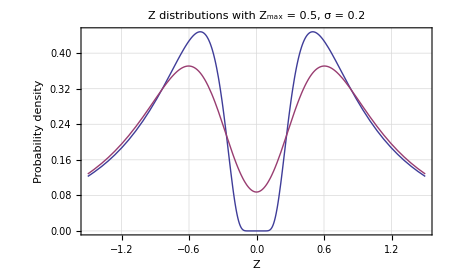

```mathematica
Zdistplot
```

```mathematica
?Zdist
```

Zdist[Z,Z_max] calculates the Z probability distribution at position Z, given the position for the positive maximum Z_max. The total area under the curve over (-∞,∞) is 1.

```mathematica
?Zconv
```

Zconv[Z,Z_max,σ] is the convolution of Zdist[Z,Z_max] with a Gaussian beam with standard deviation σ. It calculates the convolved probability distribution at position Z, given the position for the (unconvolved) positive maximum Z_max. The total area under the curve over (-∞,∞) is 1.

 Valid ranges for parameters:
 -4.0 < Z < 4.0
 0.1 < Z_max < 3.0
 0.05 < σ < 0.3

This function interpolates compressed data in the file "ConvolvedZdistribution.dat"

```mathematica
?ZconvMax
```

ZconvMax[Z_max,σ] is the Z position of the maximum of the convolution Zconv[Z,Z_max,σ].

 Valid ranges for parameters:
 0.1 < Z_max < 3.0
 0.05 < σ < 0.3

```mathematica
?FwhmToSigma
```

FwhmToSigma[w] converts w, the "Full-width at Half-maximum" of the 0-field beam, to an equivalent standard deviation σ, assuming the beam shape is Gaussian.

## Initialization Code

### Normalized Z Distribution Function (Z_max=1)

```mathematica
ZdistNorm[z_]:=Abs[z]^-3 Exp[3(1-1/Abs[z])]9/(2E^3)
```

### Z Distribution Function (area = 1)

```mathematica
Zdist[z_,zmax_]:=ZdistNorm[z/zmax]/zmax
Zdist::usage="Zdist[Z,Z_max] calculates the Z probability distribution at position Z, given the position for the positive maximum Z_max. The total area under the curve over (-∞,∞) is 1."
```

Zdist[Z,Z_max] calculates the Z probability distribution at position Z, given the position for the positive maximum Z_max. The total area under the curve over (-∞,∞) is 1.

### Z Convolved with Gaussian (from file data)

```mathematica
Zconv (*[z, zmax, sig]*)=Interpolation[Uncompress[Get[ToFileName[NotebookDirectory[],"ConvolvedZdistribution.dat"]]]];
Zconv::usage="Zconv[Z,Z_max,σ] is the convolution of Zdist[Z,Z_max] with a Gaussian beam with standard deviation σ. It calculates the convolved probability distribution at position Z, given the position for the (unconvolved) positive maximum Z_max. The total area under the curve over (-∞,∞) is 1.\n\n Valid ranges for parameters:\n -4.0 < Z < 4.0\n 0.1 < Z_max < 3.0\n 0.05 < σ < 0.6\n\nThis function interpolates compressed data in the file \"ConvolvedZdistribution.dat\""
```

Zconv[Z,Z_max,σ] is the convolution of Zdist[Z,Z_max] with a Gaussian beam with standard deviation σ. It calculates the convolved probability distribution at position Z, given the position for the (unconvolved) positive maximum Z_max. The total area under the curve over (-∞,∞) is 1.

 Valid ranges for parameters:
 -4.0 < Z < 4.0
 0.1 < Z_max < 3.0
 0.05 < σ < 0.6

This function interpolates compressed data in the file "ConvolvedZdistribution.dat"

```mathematica
ZconvMax[zmax_,sig_]:=z/.Last[Quiet[FindMaximum[Zconv[z,zmax,sig],{z,zmax}]]]
ZconvMax::usage="ZconvMax[Z_max,σ] is the Z position of the maximum of the convolution Zconv[Z,Z_max,σ].\n\n Valid ranges for parameters:\n 0.1 < Z_max < 3.0\n 0.05 < σ < 0.6"
```

ZconvMax[Z_max,σ] is the Z position of the maximum of the convolution Zconv[Z,Z_max,σ].

 Valid ranges for parameters:
 0.1 < Z_max < 3.0
 0.05 < σ < 0.6

```mathematica
FwhmToSigma[width_]:=width/(2.0Sqrt[2Log[2]])
FwhmToSigma::usage="FwhmToSigma[w] converts w, the \"Full-width at Half-maximum\" of the 0-field beam, to an equivalent standard deviation σ, assuming the beam shape is Gaussian."
```

FwhmToSigma[w] converts w, the "Full-width at Half-maximum" of the 0-field beam, to an equivalent standard deviation σ, assuming the beam shape is Gaussian.

### The plot

```mathematica
Zdistplot=Plot[{Tooltip[Zdist[z,.5],"Ideal distribution"],Tooltip[Zconv[z,.5,.2],"Finite beam width"]},{z,-1.5,1.5},Frame->True,PlotLabel->Style["Z distributions with Z_max = 0.5, σ = 0.2",Larger],GridLines->Automatic,GridLinesStyle->GrayLevel[.85],PlotStyle->Thick,FrameLabel->{Style["Z",Larger,Italic],Style["Probability density",Larger,Italic]},ImageSize->450];
```

### Here is a dynamic calculator of the distributions in a dialog window

```mathematica
ZdistNotebook=Notebook[{}];
```

```mathematica
ZdistDialog :=If[ZdistNotebook===Notebook[{}],
ZdistNotebook=CreateDialog[
{Manipulate[
Block[{s},
s=width/(2Sqrt[2Log[2]]);
Column[{
Grid[{
{Tooltip[Style["Width (FWHM, mm): ",FontFamily->"Helvetica"],"0-field beam full width at 1/2 maximum"],Tooltip[Style[ToString[ Round[width,.001]],FontFamily->"Helvetica"],"0-field beam full width at 1/2 maximum"],Tooltip[Style["Sigma (mm): ",FontFamily->"Helvetica"],"0-field beam sigma"],Tooltip[Style[ToString[ Round[s,.001]],FontFamily->"Helvetica"],"Selected 0-field beam sigma"]},{Tooltip[Style["Z_max (mm): ",FontFamily->"Helvetica"],"Ideal distribution Z_max"],Tooltip[Style[ToString[ Round[zmax,.001]],FontFamily->"Helvetica"],"Selected ideal distribution Z_max"],Tooltip[Style["Z_max (finite σ): ",FontFamily->"Helvetica"],"Z_max when convolved with beam"],Tooltip[Style[ToString[ Round[ZconvMax[zmax,s],.001]],FontFamily->"Helvetica"],"Z_max when convolved with beam"]},{}
},Alignment->{Left,Baseline},ItemSize->{{Automatic,6,Automatic,6}}](* Grid *),Plot[{Tooltip[Zdist[z,zmax],"Ideal distribution"],Tooltip[Zconv[z,zmax,s],"Finite beam width"]},{z,- Min[4,5zmax],Min[4,5zmax]},Frame->True,GridLines->Automatic,GridLinesStyle->GrayLevel[.85],PlotStyle->Thick,FrameLabel->{Style["Z",Larger,Italic],Style["Probability density",Larger,Italic]},ImageSize->400,PlotRange->All]
}] (* Column *)
](* Block *),
Style["Select desired Z_max and Beam width",Larger],
Style["Hold the 'Alt'(Windows)/'Option'(Mac) key to slow the slider action when adjusting",Smaller],"",
{{zmax,1,Tooltip["Z_max","Position of the ideal beam maximum"]},.1,3},{{width,.2(2Sqrt[2Log[2]]),Tooltip["Width","Width of the 0-field beam"]},.05(2Sqrt[2Log[2]]),.599(2Sqrt[2Log[2]])},
AppearanceElements->None](* Manipulate *)
},
Magnification->1.4,
Deployed->True,ShowCellBracket->False,Saveable->False,
WindowSize->All (*,WindowFrame->"Normal",WindowElements->"MagnificationPopUp" *),WindowFloating->False,
WindowTitle->"Z Distribution - Physics 7 Stern-Gerlach",
NotebookEventActions->{"WindowClose":>(ZdistNotebook=Notebook[{}];)}
];,SetSelectedNotebook[ZdistNotebook]];
```